1.10732×10^-6+2.06738×10^-13 x-8.52425×10^-21 x^2

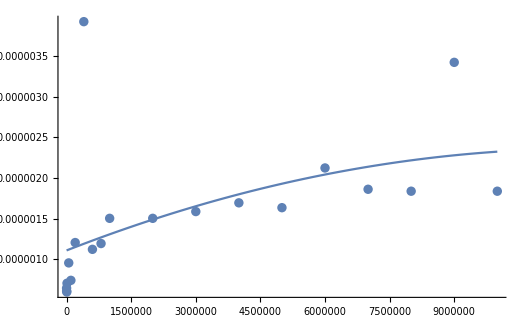

```mathematica
ABB=Fit[{{100,6.4373*10^-7},{1000,6.07967*10^-7},{5000,5.96046*10^-7},{10000,7.03335*10^-7},{50000,9.53674*10^-7},{100000,7.39098*10^-7},{200000,1.20401*10^-6},{400000,3.92199*10^-6},{600000,1.12057*10^-6},{800000,1.19209*10^-6},{1000000,1.50204*10^-6},{2000000,1.50204*10^-6},{3000000,1.58548*10^-6},{4000000,1.692775*10^-6},{5000000,1.63317*10^-6},{6000000,2.12193*10^-6},{7000000,1.85966*10^-6},{8000000,1.83582*10^-6},{9000000,3.42131*10^-6},{10000000,1.83582*10^-6}},{1,x, x^2},x]

puntosABB=ListPlot[{{100,6.4373*10^-7},{1000,6.07967*10^-7},{5000,5.96046*10^-7},{10000,7.03335*10^-7},{50000,9.53674*10^-7},{100000,7.39098*10^-7},{200000,1.20401*10^-6},{400000,3.92199*10^-6},{600000,1.12057*10^-6},{800000,1.19209*10^-6},{1000000,1.50204*10^-6},{2000000,1.50204*10^-6},{3000000,1.58548*10^-6},{4000000,1.692775*10^-6},{5000000,1.63317*10^-6},{6000000,2.12193*10^-6},{7000000,1.85966*10^-6},{8000000,1.83582*10^-6},{9000000,3.42131*10^-6},{10000000,1.83582*10^-6}}]

g1=Plot[ABB,{x,0,10000000}]
Show[puntosABB,g1,PlotRange->All]
```